```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 11586 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[ℒ]
ℒ = 1/2 m ( x'[t]^2 - ω^2 x[t]^2 ) Exp[ γ t ]  ;
ℒ // pdConv
```

1/2 m ⅇ^(γ t) (((∂x(t))/(∂t))^2-ω^2 (x(t))^2)

```mathematica
Clear[q]
q = x[t]
```

x[t]

```mathematica
D[ ℒ , D[q, t]] - D[ ℒ , q ]
```

ⅇ^(t γ) m ω^2 x[t]+ⅇ^(t γ) m x'[t]

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] ;
eqs // pdConv
```

m (-ⅇ^(γ t)) ((∂^2 x(t))/(∂t^2)+γ (∂x(t))/(∂t)+ω^2 x(t))==0

```mathematica
Clear[parameters]
parameters = { 
m-> 100 , 
γ-> 0.5 , 
ω-> 2 
} ;
parameters // TableForm
```

m→100
γ→0.5
ω→2

```mathematica
eqs /. parameters  // Expand
```

-400 ⅇ^(0.5 t) x[t]-50. ⅇ^(0.5 t) x'[t]-100 ⅇ^(0.5 t) x''[t]==0

```mathematica
Clear[ics]
ics = { 
x[0] == 0 , 
x'[0] == 10 
} ;
ics // TableForm
```

x[0]==0
x'[0]==10

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ { eqs  } /. parameters , ics ] , q , { t, 0, 100 } ] ]
```

{x[t]→InterpolatingFunction[…][t]}

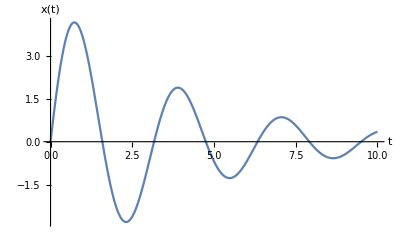

```mathematica
Plot[ Evaluate[ q /. solution[t] ] , { t, 0, 10 } , AxesLabel-> { t , q }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , PlotRange-> 10 , AxesLabel-> { q , D[q, t] } ]  ,
{ tmax , 1 ,20 , 0.5  } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 20, tmax } , AxesLabel-> { q , D[q, t] } ]  ,
{ tmax , 21 ,40 , 0.5  } ]
```

```mathematica
q
p[q]
```

x[t]

p[x[t]]

```mathematica
Map[p,q] (* No idea why this is backwards, one element ? *)
```

x[p[t]]

```mathematica
p[q]
```

p[x[t]]

```mathematica
Clear[momenta]
momenta = 
Flatten[Solve[ D[ ℒ , D[q, t] ] == p[q], x'[t]]]
```

{x'[t]→(ⅇ^(-t γ) p[x[t]])/m}

```mathematica
Clear[ℋ]
ℋ = 
( p[q] D[q, t] - ℒ  ) /. momenta // Expand
```

(ⅇ^(-t γ) p[x[t]]^2)/(2 m)+1/2 ⅇ^(t γ) m ω^2 x[t]^2

```mathematica
Clear[trial]
trial = 
x[t] -> Exp[ ⅈ Ω t ]
```

x[t]→ⅇ^(ⅈ t Ω)

```mathematica
D[trial, t]
```

x'[t]→ⅈ ⅇ^(ⅈ t Ω) Ω

```mathematica
D[D[trial, t], t]
```

x''[t]→-ⅇ^(ⅈ t Ω) Ω^2

```mathematica
eqs /. trial
```

-ⅇ^(t γ) m (ⅇ^(ⅈ t Ω) ω^2+γ x'[t]+x''[t])==0

```mathematica
eqs /. trial  /. D[trial, t]
```

-ⅇ^(t γ) m (ⅇ^(ⅈ t Ω) ω^2+ⅈ ⅇ^(ⅈ t Ω) γ Ω+x''[t])==0

```mathematica
eqs /. trial  /. D[trial, t]  /. D[D[trial, t], t]
```

-ⅇ^(t γ) m (ⅇ^(ⅈ t Ω) ω^2+ⅈ ⅇ^(ⅈ t Ω) γ Ω-ⅇ^(ⅈ t Ω) Ω^2)==0

```mathematica
Simplify[ eqs /. trial  /. D[trial, t]  /. D[D[trial, t], t]  ] 
Simplify[ eqs /. trial  /. D[trial, t]  /. D[D[trial, t], t]  ] [[1,3]]
```

ⅇ^(t (γ+ⅈ Ω)) m (-ω^2+Ω (-ⅈ γ+Ω))==0

-ω^2+Ω (-ⅈ γ+Ω)

```mathematica
Flatten[Solve[ Simplify[ eqs /. trial  /. D[trial, t]  /. D[D[trial, t], t]  ] [[1,3]] == 0 , Ω ] ]
```

{Ω→1/2 (ⅈ γ-√(-γ^2+4 ω^2)),Ω→1/2 (ⅈ γ+√(-γ^2+4 ω^2))}